#### maximum expansion order

```mathematica
ω=1000;
```

```mathematica
avector=Table[Cos[j θ],{j,0,ω}];
bvector=Join[avector,Table[Sin[j θ],{j,ω}]];
```

```mathematica
masterA=Table[
Simplify[avector/.θ->Θ[[k]]]
,{k,m}];
```

```mathematica
ν=3;
index=ν-2;
λ=Round[𝕔/(ν 1000000)];
rcs=meanRCS[[index]];
m=Length[rcs];
(* center nose angle *)
σ=RotateLeft[rcs,180];
(* characterize data set *)
μ=Mean[σ];
mx=Max[σ];
mn=Min[σ];
{top,bot}={1.1mx,0.9mn};
subtitle="ν = "<>ToString[ν]<>" MHz";
subtitle=subtitle<>", λ = "<>ToString[λ]<>" m";
Print[lf,"frequency = ",ν," MHz (λ = ", λ, " m)"];
Print["mean rcs = ",μ];
(* scatter plot of data points *)
z={Θ,σ}ᵀ;
g000=ListPlot[z,PlotStyle->{Purple,Opacity[0.5],PointSize[0.005]}];
(* initializations *)
te={};
minTE=∞;
maxerrors={};
myAmplitudes={};
myErrors={};
G={};
(* sweep expansion orders *)
$tick;
Do[
(* define Hilbert space basis functions *)
vector=avector;
(* grab slice of master matrix *)
A=masterA;
(* compute Fourier-Bessel coefficients *)
c=LeastSquares[A,σ];
AppendTo[myAmplitudes,c];
(* approximation function *)
Clear[f];
f[θ_]=c.vector;
Print["f[θ] = ",f[θ]];
(* approximation vector *)
F=f[θ]/.θ->Θ;
(* residual error *)
r=σ-F;
(* maximum error *)
emax=Norm[r,∞];
maxerrors=AppendTo[maxerrors,{d,emax}];
(* total error *)
r2=r.r;
If[r2<minTE,minTE=r2;where=d];
AppendTo[te,r2];
(* uncertainty propagation *)
ϵ=√(r2/(m-(d+1))Diagonal[Inverse[A†.A//N]]);
AppendTo[myErrors,ϵ];
(* signal to noise *)
γ=Last[c]/Last[ϵ];
AppendTo[G,{d,γ}];
(* function *)
g001=Plot[f[θ],{θ,-π,π},
Frame->True,
PlotRange->{bot,top},
FrameTicks->fticks,
PlotStyle->{Opacity[0.25],Blue}];
(* compare *)
dsubtitle=subtitle<>", d = "<>ToString[d];
ga=Show[{g001,g000},
PlotLabel->sty["MoM RCS vs Fourier Cosine Expansion"<>lf<>dsubtitle],
FrameLabel->{sty["Yaw angle, α"],sty["Mean total RCS, <σ_T>"]},
isize];
(* residual error *)
gb=ListPlot[r,
Frame->True,
FrameTicks->fticks,
FrameLabel->{sty["Nose angle"],sty["Residual error"]},
PlotRange->Λ{-1,1},
PlotStyle->{Red,PointSize[0.005]},
PlotLabel->sty["Fourier Approximation Error"<>lf<>dsubtitle],
isize];
(* group plots *)
gout=GraphicsRow[{ga,gb},
ImageSize->12 72];
(* output *)
tresExport["fit-rcs-cos-"<>pad[ν]<>"-"<>pad[d],ga];
tresExport["rcs-cos-"<>pad[ν]<>"-"<>pad[d],gout];
,{d,ω,ω}];
```

frequency = 3 MHz (λ = 100 m)

mean rcs = 35.2488

f[θ] = 11.7457+0.335019 Cos[θ]-0.686873 Cos[2 θ]-0.173266 Cos[3 θ]+1.0736 Cos[4 θ]-0.255889 Cos[5 θ]+0.275751 Cos[6 θ]-0.0732928 Cos[7 θ]+0.0370922 Cos[8 θ]+0.0132936 Cos[9 θ]-0.0221625 Cos[10 θ]+0.00960442 Cos[11 θ]-0.00722944 Cos[12 θ]-0.000750953 Cos[13 θ]+0.00148195 Cos[14 θ]-0.00293628 Cos[15 θ]+0.00178135 Cos[16 θ]-0.0016906 Cos[17 θ]+0.00049002 Cos[18 θ]-0.000679923 Cos[19 θ]+0.0000164725 Cos[20 θ]-0.000443707 Cos[21 θ]+0.0000567672 Cos[22 θ]-0.000468302 Cos[23 θ]+0.000142643 Cos[24 θ]-0.000444134 Cos[25 θ]+0.000143648 Cos[26 θ]-0.000378149 Cos[27 θ]+0.000113427 Cos[28 θ]-0.000312574 Cos[29 θ]+0.0000925641 Cos[30 θ]-0.000269231 Cos[31 θ]+0.0000820459 Cos[32 θ]-0.000237923 Cos[33 θ]+0.0000764155 Cos[34 θ]-0.00021188 Cos[35 θ]+0.0000697458 Cos[36 θ]-0.000189375 Cos[37 θ]+0.0000639587 Cos[38 θ]-0.000169513 Cos[39 θ]+0.0000584615 Cos[40 θ]-0.000153027 Cos[41 θ]+0.000054367 Cos[42 θ]-0.000138806 Cos[43 θ]+0.000050331 Cos[44 θ]-0.000126462 Cos[45 θ]+0.0000472059 Cos[46 θ]-0.000115719 Cos[47 θ]+0.0000442824 Cos[48 θ]-0.000106438 Cos[49 θ]+0.000041556 Cos[50 θ]-0.0000981107 Cos[51 θ]+0.0000391563 Cos[52 θ]-0.00009083 Cos[53 θ]+0.0000373263 Cos[54 θ]-0.0000841631 Cos[55 θ]+0.0000351861 Cos[56 θ]-0.0000784413 Cos[57 θ]+0.0000335482 Cos[58 θ]-0.000073046 Cos[59 θ]+0.000031771 Cos[60 θ]-0.0000684758 Cos[61 θ]+0.000030438 Cos[62 θ]-0.0000642996 Cos[63 θ]+0.000029165 Cos[64 θ]-0.0000604214 Cos[65 θ]+0.0000278655 Cos[66 θ]-0.0000569596 Cos[67 θ]+0.0000267715 Cos[68 θ]-0.0000538056 Cos[69 θ]+0.0000255811 Cos[70 θ]-0.0000510499 Cos[71 θ]+0.000024951 Cos[72 θ]-0.0000483299 Cos[73 θ]+0.0000240498 Cos[74 θ]-0.0000458635 Cos[75 θ]+0.0000231371 Cos[76 θ]-0.000043637 Cos[77 θ]+0.0000225825 Cos[78 θ]-0.0000414946 Cos[79 θ]+0.0000180751 Cos[80 θ]-0.0000330085 Cos[81 θ]+0.0000174458 Cos[82 θ]-0.0000317169 Cos[83 θ]+0.0000170833 Cos[84 θ]-0.0000302696 Cos[85 θ]+0.0000163929 Cos[86 θ]-0.0000290532 Cos[87 θ]+0.0000159484 Cos[88 θ]-0.0000279133 Cos[89 θ]+0.0000157272 Cos[90 θ]-0.0000269115 Cos[91 θ]+0.0000151278 Cos[92 θ]-0.0000257924 Cos[93 θ]+0.0000147303 Cos[94 θ]-0.000024908 Cos[95 θ]+0.0000144892 Cos[96 θ]-0.0000239935 Cos[97 θ]+0.0000140878 Cos[98 θ]-0.0000231824 Cos[99 θ]+0.000013736 Cos[100 θ]-0.000022481 Cos[101 θ]+0.0000135047 Cos[102 θ]-0.0000217256 Cos[103 θ]+0.0000133647 Cos[104 θ]-0.0000210826 Cos[105 θ]+0.000013012 Cos[106 θ]-0.0000202773 Cos[107 θ]+0.0000126836 Cos[108 θ]-0.0000197456 Cos[109 θ]+0.0000126034 Cos[110 θ]-0.000019147 Cos[111 θ]+0.0000123759 Cos[112 θ]-0.0000187395 Cos[113 θ]+0.0000122221 Cos[114 θ]-0.0000182447 Cos[115 θ]+0.0000120421 Cos[116 θ]-0.0000177294 Cos[117 θ]+0.0000117281 Cos[118 θ]-0.0000172653 Cos[119 θ]+0.0000117139 Cos[120 θ]-0.0000169206 Cos[121 θ]+0.000011475 Cos[122 θ]-0.0000164697 Cos[123 θ]+0.0000113368 Cos[124 θ]-0.0000160445 Cos[125 θ]+0.0000112188 Cos[126 θ]-0.0000157448 Cos[127 θ]+0.0000110586 Cos[128 θ]-0.0000154557 Cos[129 θ]+0.0000108936 Cos[130 θ]-0.0000150798 Cos[131 θ]+0.0000111171 Cos[132 θ]-0.000014739 Cos[133 θ]+0.000010737 Cos[134 θ]-0.0000144536 Cos[135 θ]+0.0000108147 Cos[136 θ]-0.0000142435 Cos[137 θ]+0.0000106019 Cos[138 θ]-0.0000139119 Cos[139 θ]+0.0000106001 Cos[140 θ]-0.000013677 Cos[141 θ]+0.0000104563 Cos[142 θ]-0.0000135399 Cos[143 θ]+0.0000105107 Cos[144 θ]-0.0000133613 Cos[145 θ]+0.0000104114 Cos[146 θ]-0.00001299 Cos[147 θ]+0.0000104648 Cos[148 θ]-0.0000128729 Cos[149 θ]+0.0000103193 Cos[150 θ]-0.0000128617 Cos[151 θ]+0.0000102663 Cos[152 θ]-0.0000125437 Cos[153 θ]+0.0000100993 Cos[154 θ]-0.0000124729 Cos[155 θ]+0.0000102611 Cos[156 θ]-0.0000124549 Cos[157 θ]+0.0000101325 Cos[158 θ]-0.0000122509 Cos[159 θ]+0.0000100108 Cos[160 θ]-0.0000120551 Cos[161 θ]+0.0000100942 Cos[162 θ]-0.0000120222 Cos[163 θ]+0.0000100757 Cos[164 θ]-0.0000117552 Cos[165 θ]+0.0000100799 Cos[166 θ]-0.0000117948 Cos[167 θ]+0.0000100917 Cos[168 θ]-0.0000118011 Cos[169 θ]+9.95902×10^-6 Cos[170 θ]-0.0000117502 Cos[171 θ]+0.0000100057 Cos[172 θ]-0.0000117456 Cos[173 θ]+9.96076×10^-6 Cos[174 θ]-0.0000117203 Cos[175 θ]+9.96468×10^-6 Cos[176 θ]-0.0000117367 Cos[177 θ]+0.00001001 Cos[178 θ]-0.0000116516 Cos[179 θ]+9.96426×10^-6 Cos[180 θ]-0.0000116516 Cos[181 θ]+0.00001001 Cos[182 θ]-0.0000117367 Cos[183 θ]+9.96468×10^-6 Cos[184 θ]-0.0000117203 Cos[185 θ]+9.96076×10^-6 Cos[186 θ]-0.0000117456 Cos[187 θ]+0.0000100057 Cos[188 θ]-0.0000117502 Cos[189 θ]+9.95902×10^-6 Cos[190 θ]-0.0000118011 Cos[191 θ]+0.0000100917 Cos[192 θ]-0.0000117948 Cos[193 θ]+0.0000100799 Cos[194 θ]-0.0000117552 Cos[195 θ]+0.0000100757 Cos[196 θ]-0.0000120222 Cos[197 θ]+0.0000100942 Cos[198 θ]-0.0000120551 Cos[199 θ]+0.0000100108 Cos[200 θ]-0.0000122509 Cos[201 θ]+0.0000101325 Cos[202 θ]-0.0000124549 Cos[203 θ]+0.0000102611 Cos[204 θ]-0.0000124729 Cos[205 θ]+0.0000100993 Cos[206 θ]-0.0000125437 Cos[207 θ]+0.0000102663 Cos[208 θ]-0.0000128617 Cos[209 θ]+0.0000103193 Cos[210 θ]-0.0000128729 Cos[211 θ]+0.0000104648 Cos[212 θ]-0.00001299 Cos[213 θ]+0.0000104114 Cos[214 θ]-0.0000133613 Cos[215 θ]+0.0000105107 Cos[216 θ]-0.0000135399 Cos[217 θ]+0.0000104563 Cos[218 θ]-0.000013677 Cos[219 θ]+0.0000106001 Cos[220 θ]-0.0000139119 Cos[221 θ]+0.0000106019 Cos[222 θ]-0.0000142435 Cos[223 θ]+0.0000108147 Cos[224 θ]-0.0000144536 Cos[225 θ]+0.000010737 Cos[226 θ]-0.000014739 Cos[227 θ]+0.0000111171 Cos[228 θ]-0.0000150798 Cos[229 θ]+0.0000108936 Cos[230 θ]-0.0000154557 Cos[231 θ]+0.0000110586 Cos[232 θ]-0.0000157448 Cos[233 θ]+0.0000112188 Cos[234 θ]-0.0000160445 Cos[235 θ]+0.0000113368 Cos[236 θ]-0.0000164697 Cos[237 θ]+0.000011475 Cos[238 θ]-0.0000169206 Cos[239 θ]+0.0000117139 Cos[240 θ]-0.0000172653 Cos[241 θ]+0.0000117281 Cos[242 θ]-0.0000177294 Cos[243 θ]+0.0000120421 Cos[244 θ]-0.0000182447 Cos[245 θ]+0.0000122221 Cos[246 θ]-0.0000187395 Cos[247 θ]+0.0000123759 Cos[248 θ]-0.000019147 Cos[249 θ]+0.0000126034 Cos[250 θ]-0.0000197456 Cos[251 θ]+0.0000126836 Cos[252 θ]-0.0000202773 Cos[253 θ]+0.000013012 Cos[254 θ]-0.0000210826 Cos[255 θ]+0.0000133647 Cos[256 θ]-0.0000217256 Cos[257 θ]+0.0000135047 Cos[258 θ]-0.000022481 Cos[259 θ]+0.000013736 Cos[260 θ]-0.0000231824 Cos[261 θ]+0.0000140878 Cos[262 θ]-0.0000239935 Cos[263 θ]+0.0000144892 Cos[264 θ]-0.000024908 Cos[265 θ]+0.0000147303 Cos[266 θ]-0.0000257924 Cos[267 θ]+0.0000151278 Cos[268 θ]-0.0000269115 Cos[269 θ]+0.0000157272 Cos[270 θ]-0.0000279133 Cos[271 θ]+0.0000159484 Cos[272 θ]-0.0000290532 Cos[273 θ]+0.0000163929 Cos[274 θ]-0.0000302696 Cos[275 θ]+0.0000170833 Cos[276 θ]-0.0000317169 Cos[277 θ]+0.0000174458 Cos[278 θ]-0.0000330085 Cos[279 θ]+0.0000180751 Cos[280 θ]-0.0000414946 Cos[281 θ]+0.0000225825 Cos[282 θ]-0.000043637 Cos[283 θ]+0.0000231371 Cos[284 θ]-0.0000458635 Cos[285 θ]+0.0000240498 Cos[286 θ]-0.0000483299 Cos[287 θ]+0.000024951 Cos[288 θ]-0.0000510499 Cos[289 θ]+0.0000255811 Cos[290 θ]-0.0000538056 Cos[291 θ]+0.0000267715 Cos[292 θ]-0.0000569596 Cos[293 θ]+0.0000278655 Cos[294 θ]-0.0000604214 Cos[295 θ]+0.000029165 Cos[296 θ]-0.0000642996 Cos[297 θ]+0.000030438 Cos[298 θ]-0.0000684758 Cos[299 θ]+0.000031771 Cos[300 θ]-0.000073046 Cos[301 θ]+0.0000335482 Cos[302 θ]-0.0000784413 Cos[303 θ]+0.0000351861 Cos[304 θ]-0.0000841631 Cos[305 θ]+0.0000373263 Cos[306 θ]-0.00009083 Cos[307 θ]+0.0000391563 Cos[308 θ]-0.0000981107 Cos[309 θ]+0.000041556 Cos[310 θ]-0.000106438 Cos[311 θ]+0.0000442824 Cos[312 θ]-0.000115719 Cos[313 θ]+0.0000472059 Cos[314 θ]-0.000126462 Cos[315 θ]+0.000050331 Cos[316 θ]-0.000138806 Cos[317 θ]+0.000054367 Cos[318 θ]-0.000153027 Cos[319 θ]+0.0000584615 Cos[320 θ]-0.000169513 Cos[321 θ]+0.0000639587 Cos[322 θ]-0.000189375 Cos[323 θ]+0.0000697458 Cos[324 θ]-0.00021188 Cos[325 θ]+0.0000764155 Cos[326 θ]-0.000237923 Cos[327 θ]+0.0000820459 Cos[328 θ]-0.000269231 Cos[329 θ]+0.0000925641 Cos[330 θ]-0.000312574 Cos[331 θ]+0.000113427 Cos[332 θ]-0.000378149 Cos[333 θ]+0.000143648 Cos[334 θ]-0.000444134 Cos[335 θ]+0.000142643 Cos[336 θ]-0.000468302 Cos[337 θ]+0.0000567672 Cos[338 θ]-0.000443707 Cos[339 θ]+0.0000164725 Cos[340 θ]-0.000679923 Cos[341 θ]+0.00049002 Cos[342 θ]-0.0016906 Cos[343 θ]+0.00178135 Cos[344 θ]-0.00293628 Cos[345 θ]+0.00148195 Cos[346 θ]-0.000750953 Cos[347 θ]-0.00722944 Cos[348 θ]+0.00960442 Cos[349 θ]-0.0221625 Cos[350 θ]+0.0132936 Cos[351 θ]+0.0370922 Cos[352 θ]-0.0732928 Cos[353 θ]+0.275751 Cos[354 θ]-0.255889 Cos[355 θ]+1.0736 Cos[356 θ]-0.173266 Cos[357 θ]-0.686873 Cos[358 θ]+0.335019 Cos[359 θ]+11.7457 Cos[360 θ]+0.335019 Cos[361 θ]-0.686873 Cos[362 θ]-0.173266 Cos[363 θ]+1.0736 Cos[364 θ]-0.255889 Cos[365 θ]+0.275751 Cos[366 θ]-0.0732928 Cos[367 θ]+0.0370922 Cos[368 θ]+0.0132936 Cos[369 θ]-0.0221625 Cos[370 θ]+0.00960442 Cos[371 θ]-0.00722944 Cos[372 θ]-0.000750953 Cos[373 θ]+0.00148195 Cos[374 θ]-0.00293628 Cos[375 θ]+0.00178135 Cos[376 θ]-0.0016906 Cos[377 θ]+0.00049002 Cos[378 θ]-0.000679923 Cos[379 θ]+0.0000164725 Cos[380 θ]-0.000443707 Cos[381 θ]+0.0000567672 Cos[382 θ]-0.000468302 Cos[383 θ]+0.000142643 Cos[384 θ]-0.000444134 Cos[385 θ]+0.000143648 Cos[386 θ]-0.000378149 Cos[387 θ]+0.000113427 Cos[388 θ]-0.000312574 Cos[389 θ]+0.0000925641 Cos[390 θ]-0.000269231 Cos[391 θ]+0.0000820459 Cos[392 θ]-0.000237923 Cos[393 θ]+0.0000764155 Cos[394 θ]-0.00021188 Cos[395 θ]+0.0000697458 Cos[396 θ]-0.000189375 Cos[397 θ]+0.0000639587 Cos[398 θ]-0.000169513 Cos[399 θ]+0.0000584615 Cos[400 θ]-0.000153027 Cos[401 θ]+0.000054367 Cos[402 θ]-0.000138806 Cos[403 θ]+0.000050331 Cos[404 θ]-0.000126462 Cos[405 θ]+0.0000472059 Cos[406 θ]-0.000115719 Cos[407 θ]+0.0000442824 Cos[408 θ]-0.000106438 Cos[409 θ]+0.000041556 Cos[410 θ]-0.0000981107 Cos[411 θ]+0.0000391563 Cos[412 θ]-0.00009083 Cos[413 θ]+0.0000373263 Cos[414 θ]-0.0000841631 Cos[415 θ]+0.0000351861 Cos[416 θ]-0.0000784413 Cos[417 θ]+0.0000335482 Cos[418 θ]-0.000073046 Cos[419 θ]+0.000031771 Cos[420 θ]-0.0000684758 Cos[421 θ]+0.000030438 Cos[422 θ]-0.0000642996 Cos[423 θ]+0.000029165 Cos[424 θ]-0.0000604214 Cos[425 θ]+0.0000278655 Cos[426 θ]-0.0000569596 Cos[427 θ]+0.0000267715 Cos[428 θ]-0.0000538056 Cos[429 θ]+0.0000255811 Cos[430 θ]-0.0000510499 Cos[431 θ]+0.000024951 Cos[432 θ]-0.0000483299 Cos[433 θ]+0.0000240498 Cos[434 θ]-0.0000458635 Cos[435 θ]+0.0000231371 Cos[436 θ]-0.000043637 Cos[437 θ]+0.0000225825 Cos[438 θ]-0.0000414946 Cos[439 θ]+0.0000180751 Cos[440 θ]-0.0000330085 Cos[441 θ]+0.0000174458 Cos[442 θ]-0.0000317169 Cos[443 θ]+0.0000170833 Cos[444 θ]-0.0000302696 Cos[445 θ]+0.0000163929 Cos[446 θ]-0.0000290532 Cos[447 θ]+0.0000159484 Cos[448 θ]-0.0000279133 Cos[449 θ]+0.0000157272 Cos[450 θ]-0.0000269115 Cos[451 θ]+0.0000151278 Cos[452 θ]-0.0000257924 Cos[453 θ]+0.0000147303 Cos[454 θ]-0.000024908 Cos[455 θ]+0.0000144892 Cos[456 θ]-0.0000239935 Cos[457 θ]+0.0000140878 Cos[458 θ]-0.0000231824 Cos[459 θ]+0.000013736 Cos[460 θ]-0.000022481 Cos[461 θ]+0.0000135047 Cos[462 θ]-0.0000217256 Cos[463 θ]+0.0000133647 Cos[464 θ]-0.0000210826 Cos[465 θ]+0.000013012 Cos[466 θ]-0.0000202773 Cos[467 θ]+0.0000126836 Cos[468 θ]-0.0000197456 Cos[469 θ]+0.0000126034 Cos[470 θ]-0.000019147 Cos[471 θ]+0.0000123759 Cos[472 θ]-0.0000187395 Cos[473 θ]+0.0000122221 Cos[474 θ]-0.0000182447 Cos[475 θ]+0.0000120421 Cos[476 θ]-0.0000177294 Cos[477 θ]+0.0000117281 Cos[478 θ]-0.0000172653 Cos[479 θ]+0.0000117139 Cos[480 θ]-0.0000169206 Cos[481 θ]+0.000011475 Cos[482 θ]-0.0000164697 Cos[483 θ]+0.0000113368 Cos[484 θ]-0.0000160445 Cos[485 θ]+0.0000112188 Cos[486 θ]-0.0000157448 Cos[487 θ]+0.0000110586 Cos[488 θ]-0.0000154557 Cos[489 θ]+0.0000108936 Cos[490 θ]-0.0000150798 Cos[491 θ]+0.0000111171 Cos[492 θ]-0.000014739 Cos[493 θ]+0.000010737 Cos[494 θ]-0.0000144536 Cos[495 θ]+0.0000108147 Cos[496 θ]-0.0000142435 Cos[497 θ]+0.0000106019 Cos[498 θ]-0.0000139119 Cos[499 θ]+0.0000106001 Cos[500 θ]-0.000013677 Cos[501 θ]+0.0000104563 Cos[502 θ]-0.0000135399 Cos[503 θ]+0.0000105107 Cos[504 θ]-0.0000133613 Cos[505 θ]+0.0000104114 Cos[506 θ]-0.00001299 Cos[507 θ]+0.0000104648 Cos[508 θ]-0.0000128729 Cos[509 θ]+0.0000103193 Cos[510 θ]-0.0000128617 Cos[511 θ]+0.0000102663 Cos[512 θ]-0.0000125437 Cos[513 θ]+0.0000100993 Cos[514 θ]-0.0000124729 Cos[515 θ]+0.0000102611 Cos[516 θ]-0.0000124549 Cos[517 θ]+0.0000101325 Cos[518 θ]-0.0000122509 Cos[519 θ]+0.0000100108 Cos[520 θ]-0.0000120551 Cos[521 θ]+0.0000100942 Cos[522 θ]-0.0000120222 Cos[523 θ]+0.0000100757 Cos[524 θ]-0.0000117552 Cos[525 θ]+0.0000100799 Cos[526 θ]-0.0000117948 Cos[527 θ]+0.0000100917 Cos[528 θ]-0.0000118011 Cos[529 θ]+9.95902×10^-6 Cos[530 θ]-0.0000117502 Cos[531 θ]+0.0000100057 Cos[532 θ]-0.0000117456 Cos[533 θ]+9.96076×10^-6 Cos[534 θ]-0.0000117203 Cos[535 θ]+9.96468×10^-6 Cos[536 θ]-0.0000117367 Cos[537 θ]+0.00001001 Cos[538 θ]-0.0000116516 Cos[539 θ]+9.96426×10^-6 Cos[540 θ]-0.0000116516 Cos[541 θ]+0.00001001 Cos[542 θ]-0.0000117367 Cos[543 θ]+9.96468×10^-6 Cos[544 θ]-0.0000117203 Cos[545 θ]+9.96076×10^-6 Cos[546 θ]-0.0000117456 Cos[547 θ]+0.0000100057 Cos[548 θ]-0.0000117502 Cos[549 θ]+9.95902×10^-6 Cos[550 θ]-0.0000118011 Cos[551 θ]+0.0000100917 Cos[552 θ]-0.0000117948 Cos[553 θ]+0.0000100799 Cos[554 θ]-0.0000117552 Cos[555 θ]+0.0000100757 Cos[556 θ]-0.0000120222 Cos[557 θ]+0.0000100942 Cos[558 θ]-0.0000120551 Cos[559 θ]+0.0000100108 Cos[560 θ]-0.0000122509 Cos[561 θ]+0.0000101325 Cos[562 θ]-0.0000124549 Cos[563 θ]+0.0000102611 Cos[564 θ]-0.0000124729 Cos[565 θ]+0.0000100993 Cos[566 θ]-0.0000125437 Cos[567 θ]+0.0000102663 Cos[568 θ]-0.0000128617 Cos[569 θ]+0.0000103193 Cos[570 θ]-0.0000128729 Cos[571 θ]+0.0000104648 Cos[572 θ]-0.00001299 Cos[573 θ]+0.0000104114 Cos[574 θ]-0.0000133613 Cos[575 θ]+0.0000105107 Cos[576 θ]-0.0000135399 Cos[577 θ]+0.0000104563 Cos[578 θ]-0.000013677 Cos[579 θ]+0.0000106001 Cos[580 θ]-0.0000139119 Cos[581 θ]+0.0000106019 Cos[582 θ]-0.0000142435 Cos[583 θ]+0.0000108147 Cos[584 θ]-0.0000144536 Cos[585 θ]+0.000010737 Cos[586 θ]-0.000014739 Cos[587 θ]+0.0000111171 Cos[588 θ]-0.0000150798 Cos[589 θ]+0.0000108936 Cos[590 θ]-0.0000154557 Cos[591 θ]+0.0000110586 Cos[592 θ]-0.0000157448 Cos[593 θ]+0.0000112188 Cos[594 θ]-0.0000160445 Cos[595 θ]+0.0000113368 Cos[596 θ]-0.0000164697 Cos[597 θ]+0.000011475 Cos[598 θ]-0.0000169206 Cos[599 θ]+0.0000117139 Cos[600 θ]-0.0000172653 Cos[601 θ]+0.0000117281 Cos[602 θ]-0.0000177294 Cos[603 θ]+0.0000120421 Cos[604 θ]-0.0000182447 Cos[605 θ]+0.0000122221 Cos[606 θ]-0.0000187395 Cos[607 θ]+0.0000123759 Cos[608 θ]-0.000019147 Cos[609 θ]+0.0000126034 Cos[610 θ]-0.0000197456 Cos[611 θ]+0.0000126836 Cos[612 θ]-0.0000202773 Cos[613 θ]+0.000013012 Cos[614 θ]-0.0000210826 Cos[615 θ]+0.0000133647 Cos[616 θ]-0.0000217256 Cos[617 θ]+0.0000135047 Cos[618 θ]-0.000022481 Cos[619 θ]+0.000013736 Cos[620 θ]-0.0000231824 Cos[621 θ]+0.0000140878 Cos[622 θ]-0.0000239935 Cos[623 θ]+0.0000144892 Cos[624 θ]-0.000024908 Cos[625 θ]+0.0000147303 Cos[626 θ]-0.0000257924 Cos[627 θ]+0.0000151278 Cos[628 θ]-0.0000269115 Cos[629 θ]+0.0000157272 Cos[630 θ]-0.0000279133 Cos[631 θ]+0.0000159484 Cos[632 θ]-0.0000290532 Cos[633 θ]+0.0000163929 Cos[634 θ]-0.0000302696 Cos[635 θ]+0.0000170833 Cos[636 θ]-0.0000317169 Cos[637 θ]+0.0000174458 Cos[638 θ]-0.0000330085 Cos[639 θ]+0.0000180751 Cos[640 θ]-0.0000414946 Cos[641 θ]+0.0000225825 Cos[642 θ]-0.000043637 Cos[643 θ]+0.0000231371 Cos[644 θ]-0.0000458635 Cos[645 θ]+0.0000240498 Cos[646 θ]-0.0000483299 Cos[647 θ]+0.000024951 Cos[648 θ]-0.0000510499 Cos[649 θ]+0.0000255811 Cos[650 θ]-0.0000538056 Cos[651 θ]+0.0000267715 Cos[652 θ]-0.0000569596 Cos[653 θ]+0.0000278655 Cos[654 θ]-0.0000604214 Cos[655 θ]+0.000029165 Cos[656 θ]-0.0000642996 Cos[657 θ]+0.000030438 Cos[658 θ]-0.0000684758 Cos[659 θ]+0.000031771 Cos[660 θ]-0.000073046 Cos[661 θ]+0.0000335482 Cos[662 θ]-0.0000784413 Cos[663 θ]+0.0000351861 Cos[664 θ]-0.0000841631 Cos[665 θ]+0.0000373263 Cos[666 θ]-0.00009083 Cos[667 θ]+0.0000391563 Cos[668 θ]-0.0000981107 Cos[669 θ]+0.000041556 Cos[670 θ]-0.000106438 Cos[671 θ]+0.0000442824 Cos[672 θ]-0.000115719 Cos[673 θ]+0.0000472059 Cos[674 θ]-0.000126462 Cos[675 θ]+0.000050331 Cos[676 θ]-0.000138806 Cos[677 θ]+0.000054367 Cos[678 θ]-0.000153027 Cos[679 θ]+0.0000584615 Cos[680 θ]-0.000169513 Cos[681 θ]+0.0000639587 Cos[682 θ]-0.000189375 Cos[683 θ]+0.0000697458 Cos[684 θ]-0.00021188 Cos[685 θ]+0.0000764155 Cos[686 θ]-0.000237923 Cos[687 θ]+0.0000820459 Cos[688 θ]-0.000269231 Cos[689 θ]+0.0000925641 Cos[690 θ]-0.000312574 Cos[691 θ]+0.000113427 Cos[692 θ]-0.000378149 Cos[693 θ]+0.000143648 Cos[694 θ]-0.000444134 Cos[695 θ]+0.000142643 Cos[696 θ]-0.000468302 Cos[697 θ]+0.0000567672 Cos[698 θ]-0.000443707 Cos[699 θ]+0.0000164725 Cos[700 θ]-0.000679923 Cos[701 θ]+0.00049002 Cos[702 θ]-0.0016906 Cos[703 θ]+0.00178135 Cos[704 θ]-0.00293628 Cos[705 θ]+0.00148195 Cos[706 θ]-0.000750953 Cos[707 θ]-0.00722944 Cos[708 θ]+0.00960442 Cos[709 θ]-0.0221625 Cos[710 θ]+0.0132936 Cos[711 θ]+0.0370922 Cos[712 θ]-0.0732928 Cos[713 θ]+0.275751 Cos[714 θ]-0.255889 Cos[715 θ]+1.0736 Cos[716 θ]-0.173266 Cos[717 θ]-0.686873 Cos[718 θ]+0.335019 Cos[719 θ]+11.7457 Cos[720 θ]+0.335019 Cos[721 θ]-0.686873 Cos[722 θ]-0.173266 Cos[723 θ]+1.0736 Cos[724 θ]-0.255889 Cos[725 θ]+0.275751 Cos[726 θ]-0.0732928 Cos[727 θ]+0.0370922 Cos[728 θ]+0.0132936 Cos[729 θ]-0.0221625 Cos[730 θ]+0.00960442 Cos[731 θ]-0.00722944 Cos[732 θ]-0.000750953 Cos[733 θ]+0.00148195 Cos[734 θ]-0.00293628 Cos[735 θ]+0.00178135 Cos[736 θ]-0.0016906 Cos[737 θ]+0.00049002 Cos[738 θ]-0.000679923 Cos[739 θ]+0.0000164725 Cos[740 θ]-0.000443707 Cos[741 θ]+0.0000567672 Cos[742 θ]-0.000468302 Cos[743 θ]+0.000142643 Cos[744 θ]-0.000444134 Cos[745 θ]+0.000143648 Cos[746 θ]-0.000378149 Cos[747 θ]+0.000113427 Cos[748 θ]-0.000312574 Cos[749 θ]+0.0000925641 Cos[750 θ]-0.000269231 Cos[751 θ]+0.0000820459 Cos[752 θ]-0.000237923 Cos[753 θ]+0.0000764155 Cos[754 θ]-0.00021188 Cos[755 θ]+0.0000697458 Cos[756 θ]-0.000189375 Cos[757 θ]+0.0000639587 Cos[758 θ]-0.000169513 Cos[759 θ]+0.0000584615 Cos[760 θ]-0.000153027 Cos[761 θ]+0.000054367 Cos[762 θ]-0.000138806 Cos[763 θ]+0.000050331 Cos[764 θ]-0.000126462 Cos[765 θ]+0.0000472059 Cos[766 θ]-0.000115719 Cos[767 θ]+0.0000442824 Cos[768 θ]-0.000106438 Cos[769 θ]+0.000041556 Cos[770 θ]-0.0000981107 Cos[771 θ]+0.0000391563 Cos[772 θ]-0.00009083 Cos[773 θ]+0.0000373263 Cos[774 θ]-0.0000841631 Cos[775 θ]+0.0000351861 Cos[776 θ]-0.0000784413 Cos[777 θ]+0.0000335482 Cos[778 θ]-0.000073046 Cos[779 θ]+0.000031771 Cos[780 θ]-0.0000684758 Cos[781 θ]+0.000030438 Cos[782 θ]-0.0000642996 Cos[783 θ]+0.000029165 Cos[784 θ]-0.0000604214 Cos[785 θ]+0.0000278655 Cos[786 θ]-0.0000569596 Cos[787 θ]+0.0000267715 Cos[788 θ]-0.0000538056 Cos[789 θ]+0.0000255811 Cos[790 θ]-0.0000510499 Cos[791 θ]+0.000024951 Cos[792 θ]-0.0000483299 Cos[793 θ]+0.0000240498 Cos[794 θ]-0.0000458635 Cos[795 θ]+0.0000231371 Cos[796 θ]-0.000043637 Cos[797 θ]+0.0000225825 Cos[798 θ]-0.0000414946 Cos[799 θ]+0.0000180751 Cos[800 θ]-0.0000330085 Cos[801 θ]+0.0000174458 Cos[802 θ]-0.0000317169 Cos[803 θ]+0.0000170833 Cos[804 θ]-0.0000302696 Cos[805 θ]+0.0000163929 Cos[806 θ]-0.0000290532 Cos[807 θ]+0.0000159484 Cos[808 θ]-0.0000279133 Cos[809 θ]+0.0000157272 Cos[810 θ]-0.0000269115 Cos[811 θ]+0.0000151278 Cos[812 θ]-0.0000257924 Cos[813 θ]+0.0000147303 Cos[814 θ]-0.000024908 Cos[815 θ]+0.0000144892 Cos[816 θ]-0.0000239935 Cos[817 θ]+0.0000140878 Cos[818 θ]-0.0000231824 Cos[819 θ]+0.000013736 Cos[820 θ]-0.000022481 Cos[821 θ]+0.0000135047 Cos[822 θ]-0.0000217256 Cos[823 θ]+0.0000133647 Cos[824 θ]-0.0000210826 Cos[825 θ]+0.000013012 Cos[826 θ]-0.0000202773 Cos[827 θ]+0.0000126836 Cos[828 θ]-0.0000197456 Cos[829 θ]+0.0000126034 Cos[830 θ]-0.000019147 Cos[831 θ]+0.0000123759 Cos[832 θ]-0.0000187395 Cos[833 θ]+0.0000122221 Cos[834 θ]-0.0000182447 Cos[835 θ]+0.0000120421 Cos[836 θ]-0.0000177294 Cos[837 θ]+0.0000117281 Cos[838 θ]-0.0000172653 Cos[839 θ]+0.0000117139 Cos[840 θ]-0.0000169206 Cos[841 θ]+0.000011475 Cos[842 θ]-0.0000164697 Cos[843 θ]+0.0000113368 Cos[844 θ]-0.0000160445 Cos[845 θ]+0.0000112188 Cos[846 θ]-0.0000157448 Cos[847 θ]+0.0000110586 Cos[848 θ]-0.0000154557 Cos[849 θ]+0.0000108936 Cos[850 θ]-0.0000150798 Cos[851 θ]+0.0000111171 Cos[852 θ]-0.000014739 Cos[853 θ]+0.000010737 Cos[854 θ]-0.0000144536 Cos[855 θ]+0.0000108147 Cos[856 θ]-0.0000142435 Cos[857 θ]+0.0000106019 Cos[858 θ]-0.0000139119 Cos[859 θ]+0.0000106001 Cos[860 θ]-0.000013677 Cos[861 θ]+0.0000104563 Cos[862 θ]-0.0000135399 Cos[863 θ]+0.0000105107 Cos[864 θ]-0.0000133613 Cos[865 θ]+0.0000104114 Cos[866 θ]-0.00001299 Cos[867 θ]+0.0000104648 Cos[868 θ]-0.0000128729 Cos[869 θ]+0.0000103193 Cos[870 θ]-0.0000128617 Cos[871 θ]+0.0000102663 Cos[872 θ]-0.0000125437 Cos[873 θ]+0.0000100993 Cos[874 θ]-0.0000124729 Cos[875 θ]+0.0000102611 Cos[876 θ]-0.0000124549 Cos[877 θ]+0.0000101325 Cos[878 θ]-0.0000122509 Cos[879 θ]+0.0000100108 Cos[880 θ]-0.0000120551 Cos[881 θ]+0.0000100942 Cos[882 θ]-0.0000120222 Cos[883 θ]+0.0000100757 Cos[884 θ]-0.0000117552 Cos[885 θ]+0.0000100799 Cos[886 θ]-0.0000117948 Cos[887 θ]+0.0000100917 Cos[888 θ]-0.0000118011 Cos[889 θ]+9.95902×10^-6 Cos[890 θ]-0.0000117502 Cos[891 θ]+0.0000100057 Cos[892 θ]-0.0000117456 Cos[893 θ]+9.96076×10^-6 Cos[894 θ]-0.0000117203 Cos[895 θ]+9.96468×10^-6 Cos[896 θ]-0.0000117367 Cos[897 θ]+0.00001001 Cos[898 θ]-0.0000116516 Cos[899 θ]+9.96426×10^-6 Cos[900 θ]-0.0000116516 Cos[901 θ]+0.00001001 Cos[902 θ]-0.0000117367 Cos[903 θ]+9.96468×10^-6 Cos[904 θ]-0.0000117203 Cos[905 θ]+9.96076×10^-6 Cos[906 θ]-0.0000117456 Cos[907 θ]+0.0000100057 Cos[908 θ]-0.0000117502 Cos[909 θ]+9.95902×10^-6 Cos[910 θ]-0.0000118011 Cos[911 θ]+0.0000100917 Cos[912 θ]-0.0000117948 Cos[913 θ]+0.0000100799 Cos[914 θ]-0.0000117552 Cos[915 θ]+0.0000100757 Cos[916 θ]-0.0000120222 Cos[917 θ]+0.0000100942 Cos[918 θ]-0.0000120551 Cos[919 θ]+0.0000100108 Cos[920 θ]-0.0000122509 Cos[921 θ]+0.0000101325 Cos[922 θ]-0.0000124549 Cos[923 θ]+0.0000102611 Cos[924 θ]-0.0000124729 Cos[925 θ]+0.0000100993 Cos[926 θ]-0.0000125437 Cos[927 θ]+0.0000102663 Cos[928 θ]-0.0000128617 Cos[929 θ]+0.0000103193 Cos[930 θ]-0.0000128729 Cos[931 θ]+0.0000104648 Cos[932 θ]-0.00001299 Cos[933 θ]+0.0000104114 Cos[934 θ]-0.0000133613 Cos[935 θ]+0.0000105107 Cos[936 θ]-0.0000135399 Cos[937 θ]+0.0000104563 Cos[938 θ]-0.000013677 Cos[939 θ]+0.0000106001 Cos[940 θ]-0.0000139119 Cos[941 θ]+0.0000106019 Cos[942 θ]-0.0000142435 Cos[943 θ]+0.0000108147 Cos[944 θ]-0.0000144536 Cos[945 θ]+0.000010737 Cos[946 θ]-0.000014739 Cos[947 θ]+0.0000111171 Cos[948 θ]-0.0000150798 Cos[949 θ]+0.0000108936 Cos[950 θ]-0.0000154557 Cos[951 θ]+0.0000110586 Cos[952 θ]-0.0000157448 Cos[953 θ]+0.0000112188 Cos[954 θ]-0.0000160445 Cos[955 θ]+0.0000113368 Cos[956 θ]-0.0000164697 Cos[957 θ]+0.000011475 Cos[958 θ]-0.0000169206 Cos[959 θ]+0.0000117139 Cos[960 θ]-0.0000172653 Cos[961 θ]+0.0000117281 Cos[962 θ]-0.0000177294 Cos[963 θ]+0.0000120421 Cos[964 θ]-0.0000182447 Cos[965 θ]+0.0000122221 Cos[966 θ]-0.0000187395 Cos[967 θ]+0.0000123759 Cos[968 θ]-0.000019147 Cos[969 θ]+0.0000126034 Cos[970 θ]-0.0000197456 Cos[971 θ]+0.0000126836 Cos[972 θ]-0.0000202773 Cos[973 θ]+0.000013012 Cos[974 θ]-0.0000210826 Cos[975 θ]+0.0000133647 Cos[976 θ]-0.0000217256 Cos[977 θ]+0.0000135047 Cos[978 θ]-0.000022481 Cos[979 θ]+0.000013736 Cos[980 θ]-0.0000231824 Cos[981 θ]+0.0000140878 Cos[982 θ]-0.0000239935 Cos[983 θ]+0.0000144892 Cos[984 θ]-0.000024908 Cos[985 θ]+0.0000147303 Cos[986 θ]-0.0000257924 Cos[987 θ]+0.0000151278 Cos[988 θ]-0.0000269115 Cos[989 θ]+0.0000157272 Cos[990 θ]-0.0000279133 Cos[991 θ]+0.0000159484 Cos[992 θ]-0.0000290532 Cos[993 θ]+0.0000163929 Cos[994 θ]-0.0000302696 Cos[995 θ]+0.0000170833 Cos[996 θ]-0.0000317169 Cos[997 θ]+0.0000174458 Cos[998 θ]-0.0000330085 Cos[999 θ]+0.0000180751 Cos[1000 θ]

Inverse::sing: Matrix {{361.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,«7»,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,1.,-1.,«951»},{«1»},«47»,{«1»},«951»} is singular.

Diagonal::list: List expected at position 1 in Diagonal[Inverse[{«1»}]].

```mathematica
z={Range[0,ω],Abs[Last[myAmplitudes]]}ᵀ;
```

```mathematica
clrs=(If[#>0,Blue,Red])&/@Last[myAmplitudes]
Length[%]
```

1001

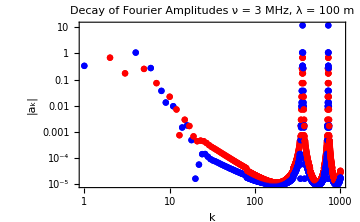

```mathematica
tbl=Table[
ListLogLogPlot[{Abs[z[[k]]]},PlotStyle->clrs[[k]]]
,{k,Length[clrs]}];
gamp=Show[tbl,
Frame->True,
Axes->False,
ImageSize->5 72,
PlotLabel->"Decay of Fourier Amplitudes"<>lf<>subtitle,
FrameLabel->{"k","|a_k|"},
PlotRange->All]
```

```mathematica
tresExport["amplitudes-"<>pad[ω,4],gamp]
```

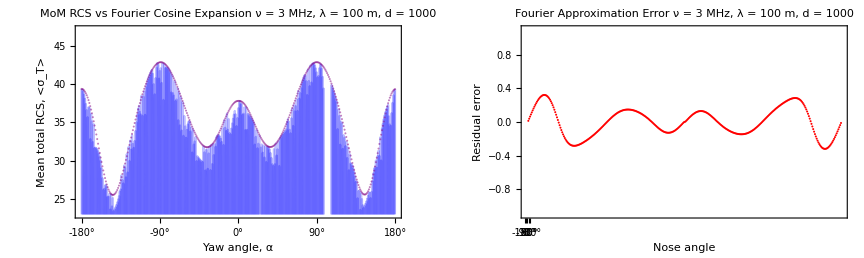

```mathematica
gout
```

```mathematica
gA=ArrayPlot[A]
```

-Graphics-

```mathematica
tresExport["A1000",gA]
```

```mathematica
Apinv=PseudoInverse[A]
```